# Simple Harmonic Motion

## Lab Report

Names: Aryan Malhotra
Section: H4
Date: 11/06/2024

## Purpose

To study the relationships of displacement, velocity, acceleration, kinetic energy, potential energy, amplitude, and frequency in simple harmonic motion (SHM) or simple harmonic oscillator (SHO), and to explore the effects of non linearity on these relationships.

## Apparatus

Computer for gathering and analyzing the data, universal lab interface, spring, weights, mass hanger, stand, motion sensor,  the protector for motion sensor.

## Readings

You can review the concepts using Wikipedia or your favorite textbook,
Simple Harmonic Motion, Error Propagation Rules

Review the least-squares fitting using Chapter 8 of John R Taylor's book or the shorter version given in Lab 3, Readings section.

### Oscillating Spring

As an example of a simple harmonic motion, let’s consider a mass, m, attached to a spring which is fixed at one end and free to slide on a frictionless surface. Mathematically, the restoring force exerted by the spring on the mass is given by Hooke’s law,
(1) 	 F = -k(x-x0).
The constant k, called the spring constant, characterizes the stiffness of the spring. A large k means a large force is needed to stretch (or compress) the spring a small distance.
The rest position is at x0 where the force is zero. The force on the mass reaches a maximum at x = ±A, where the mass momentarily stops and then moves back toward its rest position. A is called the amplitude of the oscillation.
From Newton’s law F=ma we get,
(2)	m dx^2/dt^2 = -kx.
This is a differential equation that you may not have yet learned how to solve. One of the solutions that satisfies this equation is	
(3)	x = A cos((2π)/T t),
where T is the period of the oscillation, the time it takes for the mass to complete one cycle of oscillation. Substituting Eq. (3) into Eq.(2), we the period to be:
(4)	T = 2π√(m/k).
The frequency (in Hertz) of the SHO’s oscillations is
(5) 	f = 1/T = 1/(2π)√(k/m).
Substituting Eq. (6) into Eq. (5) we get,
(6)	 x(t) = A cos√(k/m)t
Note that this solution assumes that at t = 0, x = A; the SHO starts at the positive amplitude. The velocity as a function of time is found by taking a derivative with respect to time, v=dx/dt,
(7)	 v(t) = - A√(k/m) sin√(k/m)t = A√(k/m) cos(√(k/m)t+90^o),
where we have used the identity: -sin θ = cos (θ + 90^o). The acceleration, dv/dt, is,
(8)	a(t) = −A k/mcos √(k/m)t = A k/mcos( √(k/m)t + 180^o) ,
where we have used the identity: - cos θ = cos (θ + 180^o).

By conservation of energy, the total mechanical energy of a SHO is constant,
	K.E. + P.E. =1/2 mv^2 +1/2 kx^2= constant = E
When the spring is stretched to its maximum, x = A, and the velocity, v, is zero and,
	E =1/2 kA^2 .
For any other position of the spring, x and v are both not zero and,
(9)	1/2 mv^2 +1/2 kx^2=1/2 kA^2

## Procedure

WARNING: AVOID DROPPING WEIGHTS ON THE SONIC RANGER BY OVERLOADING, EXCESSIVELY PULLING ON, OR OVERDRIVING THE SPRING. THIS WILL MAKE THE WEIGHTS FALL OFF THE HANGER, WHICH CAN DAMAGE THE DETECTOR.

The illustration above shows the experimental setup. The ULI (Universal Lab Interface) is hooked to a sonic ranger that is placed on the floor looking up at a mass hanger. The mass hanger consists of two parts whose total mass must be included in your calculations. Don’t forget this. Additional masses are placed on top of the hanger’s tilted top side. The mass hanger is attached to a spring that is suspended from a stand. The stand must be securely clamped or screwed into the table top.

## Dialog:

### Step 1. Spring Constant k

- Use masses of 50, 100, 150, 200, and 250 g to measure the CHANGE in the hanger’s height for the CHANGE in the added weight. Use LoggerPro to measure the distance.

#### Question 1. - Do you need to count the weight of the holder or spring in this step? No, we do not need to count the weight of the spring or holder in this step. We are going to measure the difference/CHANGE in height of the spring which will only depend on the masses we add on top. (F=-kx = (m+M)g = mg + Mg) Mg is going to be a constant intercept.

Find the best estimates for the spring constant k and its uncertainty. See your homework.
- The Mathematica function LinearModelFit makes a linear fit to your data and gives you the slope for the line x=x0+(g/k)m. Using this slope you can calculate the spring constant.
- Calculate the error in slope, writing the needed code below. Use that and the error propagation rules to calculate the error in k.
- Using the example in your homework make the length vs mass plot with error bars for your data. 

Initial Positions
0.000 kg - 0.279 m
0.050 kg - 0.305 m
0.100 kg - 0.332 m
0.150 kg - 0.357 m
0.200 kg - 0.384 m
0.250 kg - 0.411 m

{{0.,0.},{0.05,0.026},{0.1,0.053},{0.15,0.078},{0.2,0.105},{0.25,0.132}}

FittedModel[…]

18.6198

0.00270047

0.0954381

0.000564843

| Estimate | Standard Error | Confidence Interval
1 | -0.000190476 | 0.000408803 | {-0.0013255,0.000944544}
y | 0.526857 | 0.00270047 | {0.519359,0.534355}

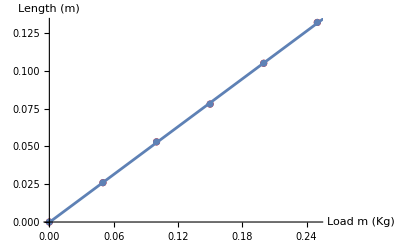

```mathematica
Needs["ErrorBarPlots`"];
xvm=Rest[{{m (Kg), x (m)}, {0.000, 0.279-0.279}, {0.050, 0.305-0.279}, {0.100, 0.332-0.279}, {0.150, 0.357-0.279}, {0.200, 0.384-0.279}, {0.250, 0.411-0.279}}]

line= LinearModelFit[xvm,y,y] (*Best fit line through least squares is x = 0.121 + 1.26m*)
fitline = line[[1,2]][[1]];
A = fitline[[1]];
B = fitline[[2]];
k = 9.81/B
paramVariances=line["ParameterErrors"]; (*sigmaA , sigmaB*)
sigmaA = paramVariances[[1]];
sigmaB = paramVariances[[2]] (*Error in Slope*)
sigmaK=(9.81/B^2)*sigmaB (*Error in Spring constant*)


(*Since x = A + Bm, sigmax = Sqrt[1/(N) * (sum(xi - A - Bmi))]*)
sigmax=  Sqrt[1/(Length[xvm]-2) * Sum[(xvm[[i]][[2]] - fitline[[1]]-fitline[[2]]*xvm[[i]][[1]])^2,{i, 1, Length[xvm]}]] (*uncertainty in the measured x value calculated by least-squares fit method*)
line["ParameterConfidenceIntervalTable"]
Show[
ListPlot[xvm,PlotStyle->Red],
Plot[line[y],{y,0,6}],
ErrorListPlot[Join[xvm,Table[{sigmax},{i,1,Length[xvm]}],2]],
AxesLabel->{"Load m (Kg)","Length (m)"}]


(*Data, 
Fitted Model, 
k, 
sigmaB, 
sigmaK, sigmax*)
```

This error plot shows that the extension of a spring is very accurately a directly proportional quantity to the load hanging from the String.
Hence, x  ∝ F

### Step 2. Theoretical Period T

- Using the spring constant k you calculated in step 1, find the theoretical value of period T for each of the above mass values from Eq. (4).
- Use the error propagation rules to find the uncertainties in your calculated values of period from uncertainty in the spring constant k.

Eq 4
T = 2π√(m/k).

k ± Δk =   18.7 ± 0.0954         (*spring constant calculated in step 1*)

```mathematica
Ttheo=Rest[{{m (Kg), T_theo(s), ΔT (s)}, {0.100, 0.460, 0.00118}, {0.150, 0.564, 0.00145}, {0.200, 0.651, 0.00167}, {0.250, 0.728, 0.00187}, {0.300, 0.798, 0.00204}, {0.350, 0.861, 0.00221}}];
```

```mathematica
For[i=0, i<Length[xvm],i++,Print[{2*Pi* Sqrt[(xvm[[i+1]][[1]]+0.100)/k], sigmaK/k*Pi *Sqrt[(xvm[[i+1]][[1]]+0.100)/k]}]]
(*T ± ΔT*)
```

{0.46046,0.00118007}

{0.563946,0.00144528}

{0.651189,0.00166887}

{0.728051,0.00186585}

{0.79754,0.00204394}

{0.861442,0.00220771}

### Step 3. Measured Period T

- For each of the masses in step 1, pull the hanger down by a small amount so that it oscillates with a full swing (double amplitude) of only 1 to 2 cm. That’s enough to get good data. Make sure it is oscillating vertically and not rocking or swinging sideways.
- Set the data rate to 40 Hz and measure about 10 seconds.
- Save your data in CSV format, import it in Mathematica and make x vs time plots for each different weight.
- In each case find the period of the oscillations by finding the time interval between n consecutive peaks and dividing this time interval by n-1. The higher the number n, the better your accuracy of determining the period T. Using n between 5 and 10 should be sufficient. 
- Find the uncertainty in your measured values of the period using the least-squares fit method.
- Using NonlinearModelFit fit your data to Eq. (4) and Show the fitted line and your data together.

FittedModel[…]

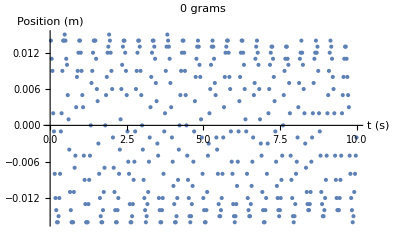

FittedModel[…]

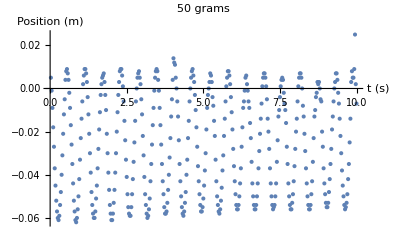

FittedModel[…]

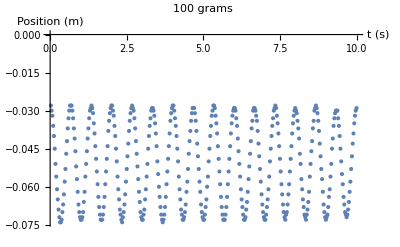

FittedModel[…]

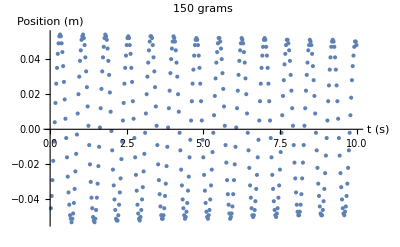

FittedModel[…]

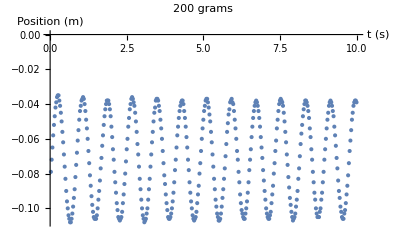

FittedModel[…]

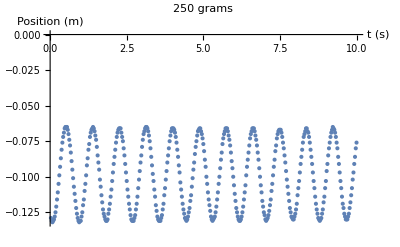

FittedModel[…]

| Estimate | Standard Error | Confidence Interval
a | 0.0452429 | 0.00371375 | {0.0349319,0.055554}
b | 1.39912 | 0.00782928 | {1.37739,1.42086}

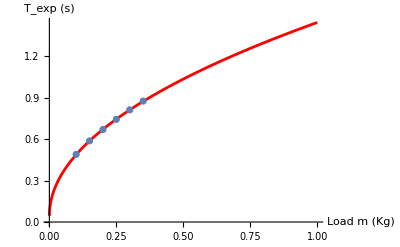

```mathematica
Needs["ErrorBarPlots`"];
data0=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 8\\lab8mass0oscillation.csv"];
nlm0=NonlinearModelFit[Take[dis0,Length[dis0]-1],offset + Amp* Cos[2Pi*t/T0 + phi],{offset,Amp,T0, phi},t]
dis0 = Rest[Part[data0, All,  {1,2}]];
ListPlot[dis0, AxesLabel->{"t (s)","Position (m)"},PlotLabel->"0 grams"]
data50=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 8\\lab8mass50oscillation.csv"];
nlm50=NonlinearModelFit[Take[dis50,Length[dis50]-1],offset + Amp* Cos[2Pi*t/T0 + phi],{offset,Amp,T0, phi},t]
dis50 = Rest[Part[data50, All,  {1,2}]];
ListPlot[dis50, AxesLabel->{"t (s)","Position (m)"},PlotLabel->"50 grams"]
data100=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 8\\lab8mass100oscillation.csv"];
nlm100=NonlinearModelFit[Take[dis100,Length[dis100]-1],offset + Amp* Cos[2Pi*t/T0 + phi],{offset,Amp,T0, phi},t]
dis100 = Rest[Part[data100, All,  {1,2}]];
ListPlot[dis100, AxesLabel->{"t (s)","Position (m)"},PlotLabel->"100 grams"]
data150=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 8\\lab8mass150oscillation.csv"];
nlm150=NonlinearModelFit[Take[dis150,Length[dis150]-1],offset + Amp* Cos[2Pi*t/T0 + phi],{offset,Amp,T0, phi},t]
dis150 = Rest[Part[data150, All,  {1,2}]];
ListPlot[dis150, AxesLabel->{"t (s)","Position (m)"},PlotLabel->"150 grams"]
data200=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 8\\lab8mass200oscillation.csv"];
nlm200=NonlinearModelFit[Take[dis200,Length[dis200]-1],offset + Amp* Cos[2Pi*t/T0 + phi],{offset,Amp,T0, phi},t]
dis200 = Rest[Part[data200, All,  {1,2}]];
ListPlot[dis200, AxesLabel->{"t (s)","Position (m)"},PlotLabel->"200 grams"]
data250=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 8\\lab8mass250oscillation.csv"];
nlm250=NonlinearModelFit[Take[dis250,Length[dis250]-1],offset + Amp* Cos[2Pi*t/T0 + phi],{offset,Amp,T0, phi},t]
dis250 = Rest[Part[data250, All,  {1,2}]];
ListPlot[dis250, AxesLabel->{"t (s)","Position (m)"},PlotLabel->"250 grams"]

Texp=Rest[{{m (Kg), T_exp(s)}, {0.100, 4.403/9}, {0.150, 5.283/9}, {0.200, 6.025/9}, {0.250, 6.686/9}, {0.300, 7.303/9}, {0.350, 7.876/9}}];
line=NonlinearModelFit[Texp,a +b y^0.5,{a,b},y]
line["ParameterConfidenceIntervalTable"]
sigmat=line["ParameterErrors"][[2]] ;(*uncertainty in the measured values of the period from the least-squares fit method*)
Show[
Plot[line[y],{y,0,1},PlotStyle->Red],
ErrorListPlot[Join[Texp,Table[{sigmat},{i,1,Length[Texp]}],2]],
AxesLabel->{"Load m (Kg)","T_exp (s)"}]
```

### Step 4. Amplitude Dependence

- For a fixed mass measure the period for oscillation with different amplitudes.

We add 50g of mass and hence the total mass hanging down from the spring is about 150g.

```mathematica
TvA=Rest[{{Amplitude (m), T_exp}, {(.019+.023)/2, 5.27/9}, {(.018+.015)/2, 4.13/7}, {(.011+.008)/2, 5.27/9}, {(.035+.031)/2, 4.693/8}, {(.026+.022)/2, 5.257/9}, {(.018+.014)/2, 4.137/7}}]
```

{{0.021,0.585556},{0.0165,0.59},{0.0095,0.585556},{0.033,0.586625},{0.024,0.584111},{0.016,0.591}}

#### Question 2. - Is there any correlation between the amplitude and period? Explain. The Experimental time periods are all about 5.86 seconds for the same mass 150g for the different amplitudes. That means that Amplitude has No correlation with the mass we hang from the spring. Even analytically, we know that the Time period is only dependent on m and k by equation 4, NOT the amplitude.

### Step 5. Comparing the measured and theoretical values of period

- Compare the measured values of period Texp with the theoretical values from Eq. (4).

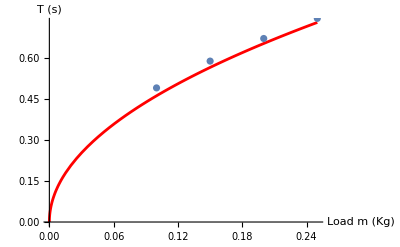

```mathematica
k=  k  ;(*spring constant calculated in step 1*)
TimeP[m1_, k_]:=2 π Sqrt[m1/k];
Show[
Plot[TimeP[m,k],{m,0,0.25},PlotStyle->Red],
ErrorListPlot[Join[Texp,Table[{sigmat},{i,1,Length[Texp]}],2]],
AxesLabel->{"Load m (Kg)","T (s)"}]
```

#### Question 3. - How well the measured and theoretical values of period agree? Explain. The measured values are very nicely fitting with theoretical values. The experiment was conducted well. The Initial Fit is a little off the predicted values however, that might be because the pendulum was really unstable for smaller values of masses. For larger mass values, the pendulum was much more stable.

Rutgers 275 Classical Physics Lab
“Simple Harmonic Motion”, contributed by Maryam Taherinejad and Girsh Blumberg ©2014
Updated by Vitaly Podzorov, Nov. 2, 2023.